## Sector Function

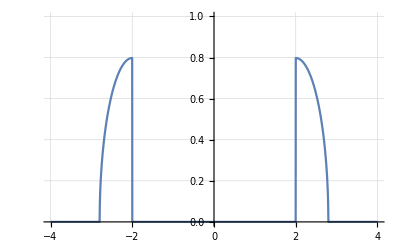

```mathematica
f[x_]:=Sqrt[2.0/π-(x+2)^2]/;-2-Sqrt[2.0/π]≤x≤-2;
f[x_]:=Sqrt[2.0/π-(x-2)^2]/;2≤x≤2+Sqrt[2.0/π];
f[x_]:=0/;x≥2+Sqrt[2.0/π];
f[x_]:=0/;x≤ -2-Sqrt[2.0/π];
f[x_]:=0/;-2≤x≤2;
Plot[f[x],{x,-4,4},PlotRange->{{-4,4},{0,1.0}},GridLines->Automatic]
```

```mathematica
Export[NotebookDirectory[]<>"Sector.dat",Table[{ω,f[ω]},{ω,-4,4,0.01}]]
```

\\Client\H$\Documents\acnotes\mbook\sector\check\Sector.dat

## Transform to Imaginary time

```mathematica
G[τ_,β_]:=NIntegrate[f[ω]Exp[-τ ω]/(1+Exp[-β ω]),{ω,-2-Sqrt[2.0/π],-2}]+NIntegrate[f[ω]Exp[-τ ω]/(1+Exp[-β ω]),{ω,2,2+Sqrt[2.0/π]}]
β=50.;
Ntau=1000;
```

```mathematica
TabulatedG=Table[{β/Ntau*n,G[β/Ntau*n,β]},{n,0,Ntau}];
Export[NotebookDirectory[]<>"SectorTime.dat",TabulatedG]
```

\\Client\H$\Documents\acnotes\mbook\sector\check\SectorTime.dat

## Transform to Matsubara Frequency

```mathematica
nmax=1000
```

1000

```mathematica
iωntable=Table[I(2n+1)π/β,{n,1,nmax}];
```

```mathematica
Giωntable=Table[NIntegrate[TripleCurve[ω]/(iωntable[[j]]-ω),{ω,-Infinity,Infinity}],{j,1,nmax}];
```

```mathematica
ωnReGiωntable=Table[{Im[iωntable[[j]]],Re[Giωntable[[j]]]},{j,1,nmax}];
ωnImGiωntable=Table[{Im[iωntable[[j]]],Im[Giωntable[[j]]]},{j,1,nmax}];
```

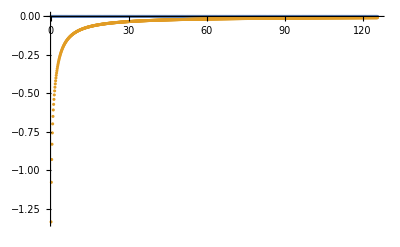

```mathematica
ListPlot[{ωnReGiωntable,ωnImGiωntable},PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"TripleGaussianFrequency.dat",ωnImGiωntable]
```

\\Client\C$\Users\tchen\Documents\acnotes\mbook\imaginary\TripleGaussianFrequency.dat

```mathematica
"/Users/tchen/Documents/acnotes/mbook/b50/TripleGaussianFrequency.dat"
```

/Users/tchen/Documents/acnotes/mbook/b50/TripleGaussianFrequency.dat